```mathematica
Manipulate[
Module[{daisy,di,Ac,P,ΔH,Ua,Ta,Cp,A,Ea,k,R,Q,r,Fao,To,Ti,s,Qloc,p1,p2,p3,p4,x1,x2,fQ,p5,v,rtBound},
daisy=Sequence[Frame->True,LabelStyle->{Black,13},ImageSize->400,ImagePadding->{{55,5},{50,10}}];

di=0.25;(*m*)
Ac=(π/4)*di^2;
P=5;(*bar*)
ΔH=If[bn==1,-1,1]*75000;
Ua=500;
Ta=400;
Cp=75;
A=0.1;
Ea=1.16*10^4;
k=A*Exp[-Ea/(8.314*(T[z]+273))];
R=8.314*10^-5;
Q=(R*(T[z]+273))/P*(Fa[z]+Fb[z]);

Fao=0.5;
To=400;

s=NDSolve[{
Fa'[z]==-(k*Fa[z])/Q*Ac,
Fb'[z]==n*(k*Fa[z])/Q*Ac,
T'[z]==Ac*((-k*Fa[z]*Ac/Q)*ΔH-Ua*(T[z]-Ta))/((Fa[z]+Fb[z])*Cp),
Fa[0]==Fao,Fb[0]==0,T[0]==To},{Fa,Fb,T},{z,0,L}];

fQ[z_]=Integrate[Q/.s,z][[1]];
Qloc[loc_]=Q/.z->loc/.s[[1]];
v[loc_]=fQ[z]/.z->loc;

p1=Plot[{Fa[z]/.s,Fb[z]/.s},{z,0,L},
PlotRange->{0,1.2},
PlotStyle->{{Thick,Blue},{Thick,RGBColor[0.,0.6,0.06]}},
FrameLabel->{Style["distance down reactor (m)",16],Style["molar flow rate (mol/s)",16]},Evaluate@daisy];

p2=Plot[T[z]/.s,{z,0,L},
PlotRange->If[bn==1,{400,407},{393,400}],
PlotStyle->{Thick,Black},
FrameLabel->{Style["distance down reactor (m)",16],Style["temperature (K)",16]},Evaluate@daisy];

p3=Show[Plot[{Q/.s,Q/.z->0/.s},{z,0,L},
PlotRange->{0,0.0145},
PlotStyle->{{Thick,Black},{Thin,Black}},
FrameLabel->{Style["distance down reactor (m)",16],Style["volumetric flow rate (m^3/s)",16]}],Evaluate@daisy];

p4=Plot[fQ[z],{z,0,L}];


x1=v[i];
x2=v[i]+10*(1.1*Qloc[i]-Qloc[0]);

rtBound=(v[L]-v[0])+10*(1.1*Qloc[L]-Qloc[0]);

p5=Graphics[{
{Thick,Line[{{-0.05*rtBound,0},{1.05*rtBound,0}}],Line[{{-0.05*rtBound,1},{1.05*rtBound,1}}]},
Rectangle[{x1,0},{x2,1}](*,
Table[{GrayLevel[0.4],Thin,Line[{{*)
},ImageSize->450,AspectRatio->1/4,(*PlotRange->{{-0.05*rtBound,1.05*rtBound},{-0.1,1.01}},*)PlotLabel->Column[{rtBound,N[rtBound/L]}],Frame->{{None,None},{True,None}}];

Show[Switch[cs,1,p1,2,p2,3,p3,4,p4,5,p5]]

],
Control[{{i,0,""},0,L,Trigger,AnimationRate->5,AppearanceElements->{"PlayPauseButton","ResetButton"}}],
Grid[{
{Control[{{cs,5,""},{1->"molar flow rate",2->"temperature",3->"volumetric flow rate",4->"velocity",5->"reactor?"},Setter}]},
{Control[{{bn,1,""},{1->"exothermic",2->"endothermic"},Setter}]}
},Alignment->Left],
Control[{{n,1.5,"product reaction coefficient"},0.5,3,0.5,Appearance->"Labeled"}],
Control[{{L,25,"reactor length (m)"},1,25,1,Appearance->"Labeled"}]
]
```

```mathematica
(*Grid[{
{Graphics[{Text@Style[
If[n==1,"A ⟶ B",Which[
n==0.5,Row[{"A ⟶ ",1/2," B"}],
n==1.5,Row[{"A ⟶ ",3/2," B"}],
n==2,"A ⟶ 2 B",
n==2.5,Row[{"A ⟶ ",5/2," B"}],
n==3,"A ⟶ 3 B"
]],17]},ImageSize->{200,50}]},
{Show[Switch[cs,1,p1,2,p2],Frame->True,LabelStyle->{Black,13},ImageSize->400,ImagePadding->{{55,5},{50,10}}]}
},Alignment->Center]*)
```

```mathematica
ImageDimensions[-Graphics-]
```

{360,360}

```mathematica
(*Grid[{
{Control[{{cs,2,""},{1->"molar flow rate",2->"temperature"},Setter}],
Control[{{bn,1,"reaction:"},{1->"exothermic",2->"endothermic"},Setter}]},
{Control[{{n,1,"product reaction coefficient"},1,3,0.5,Appearance->"Labeled"}]},
{Control[{{L,25,"reactor length (m)"},1,25,0.1,Appearance->"Labeled"}]}
},Alignment->Left]*)
```

```mathematica
(*{{A,0.1,"A"},0.01,00.1,0.01,Appearance->"Labeled"},
{{Ea,1.16*10^4,"Ea"},10,10^5,Appearance->"Labeled"},*)
```

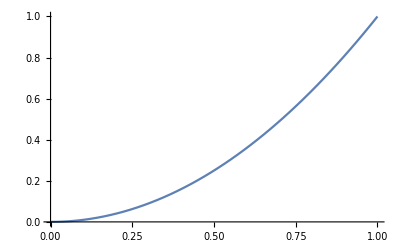

```mathematica
Plot[x^2,{x,0,1},PlotLabel->Graphics[{Text@Style[Row[{1/2," x"}],17]},ImageSize->{50,40}]]
```

```mathematica
Manipulate[
Sw
```